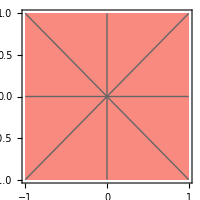
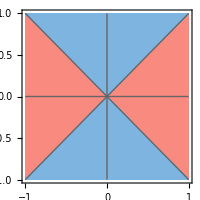
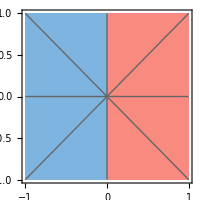
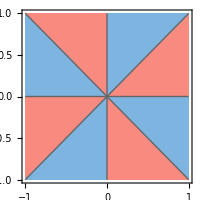
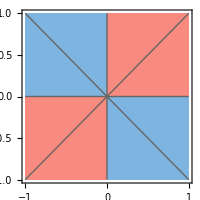
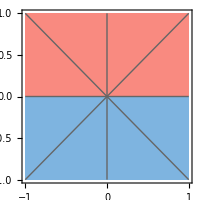
-Graphics-

A_1 : z | -Graphics-

B_1 : x^2-y^2 | -Graphics-

E : x
-Graphics-

A_2 : xy (x^2-y^2) | -Graphics-

B_2 : xy | -Graphics-

E : y

```mathematica
ClearAll[PlotIrrep,MakeLabel];


PlotIrrep[func_]:=Module[{plot,lines},plot= RegionPlot[{func[x,y]>0,func[x,y]<0},{x,-1,1},{y,-1,1},
PlotStyle->{Directive[RGBColor["#f98a80"],EdgeForm[None]],
Directive[RGBColor["#7eb4e0"],EdgeForm[None]]  },
BoundaryStyle->None,
Frame->True,
FrameTicks->None,
PlotPoints->80,
MaxRecursion->3,
ImageSize->200];
lines=Graphics[{Thin,GrayLevel[0.4],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}];
Show[plot,lines,PlotRange->{{-1,1},{-1,1}}]];


MakeLabel[text_]:=Style[TraditionalForm[text],40,FontFamily->"Times New Roman"];


cellWidth=300;
labelHeight=65;

Grid[{{Pane[Column[{PlotIrrep[1&],Spacer[5],Pane[MakeLabel[Row[{Subscript["A",1]," : ",z}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1^2-#2^2&],Spacer[5],Pane[MakeLabel[Row[{Subscript["B",1]," : ",x^2-y^2}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1&],Spacer[5],Pane[MakeLabel[Row[{"E"," : ",x}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}]},{Pane[Column[{PlotIrrep[#1 #2 (#1^2-#2^2)&],Spacer[5],Pane[MakeLabel[Row[{Subscript["A",2]," : ",xy(x^2-y^2)}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1 #2&],Spacer[5],Pane[MakeLabel[Row[{Subscript["B",2]," : ",xy}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#2&],Spacer[5],Pane[MakeLabel[Row[{"E"," : ",y}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}]}},Alignment->Center,Spacings->{1.5,1.5}]
```

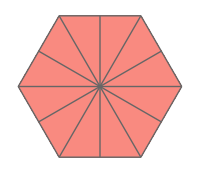
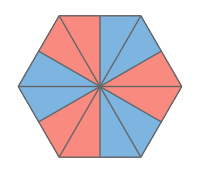
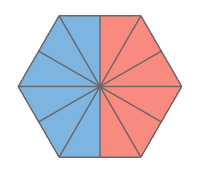
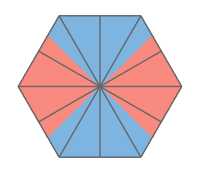
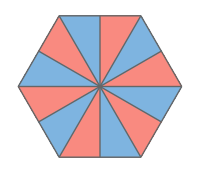
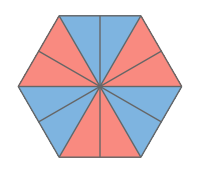
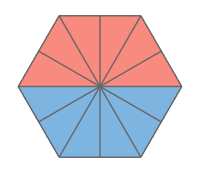
-Graphics-

A_1 : z | -Graphics-

B_1 : x (x^2-3 y^2) | -Graphics-

E_1 : x | -Graphics-

E_2 : x^2-y^2
-Graphics-

A_2 : B_1×B_2 | -Graphics-

B_2 : y (3 x^2-y^2) | -Graphics-

E_1 : y | -Graphics-

E_2 : xy

```mathematica
ClearAll[PlotIrrep,MakeLabel];

PlotIrrep[func_]:=Module[{plot,lines,hex,vertices,θ,dir,intersection},vertices={{1,0},{1/2,Sqrt[3]/2},{-1/2,Sqrt[3]/2},{-1,0},{-1/2,-Sqrt[3]/2},{1/2,-Sqrt[3]/2}};
hex=Polygon[vertices];
plot=RegionPlot[{func[x,y]>0&&Abs[x]+Abs[y]/Sqrt[3]<=1,func[x,y]<0&&Abs[x]+Abs[y]/Sqrt[3]<=1},{x,-1,1},{y,-Sqrt[3]/2,Sqrt[3]/2},
PlotStyle->{Directive[RGBColor["#f98a80"],EdgeForm[None]],Directive[RGBColor["#7eb4e0"],EdgeForm[None]]},
BoundaryStyle->None,
Frame->False,
PlotPoints->100,
MaxRecursion->3];
lines=Graphics[{Thin, GrayLevel[0.4],Table[θ=n Pi/6;
dir={Cos[θ],Sin[θ]};
intersection=RegionIntersection[Line[{-2 dir,2 dir}],hex];
intersection,{n,0,5}]}];
hex=Graphics[{Thin,GrayLevel[0.4],Line[Append[vertices,First[vertices]]]}];
Show[plot,lines,hex,PlotRange->{{-1,1},{-Sqrt[3]/2,Sqrt[3]/2}},AspectRatio->Sqrt[3]/2,ImageSize->200]];


MakeLabel[text_]:=Style[TraditionalForm[text],40,FontFamily->"Times New Roman"];



cellWidth=300;
labelHeight=65;




Grid[{{
Pane[Column[{PlotIrrep[1&],Spacer[5],Pane[MakeLabel[Row[{Subscript["A",1]," : ",z}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],
Pane[Column[{PlotIrrep[#1 (#1^2-3 #2^2)&],Spacer[5],Pane[MakeLabel[Row[{Subscript["B",1]," : ",x(x^2-3y^2)}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1&],Spacer[5],Pane[MakeLabel[Row[{Subscript["E",1]," : ",x}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1^2-#2^2&],Spacer[5],Pane[MakeLabel[Row[{Subscript["E",2]," : ",x^2-y^2}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}]},

{Pane[Column[{PlotIrrep[#1 #2 (3 #1^4-10 #1^2 #2^2+3 #2^4)&],Spacer[5],Pane[MakeLabel[Row[{Subscript["A",2]," : ",Subscript["B",1],"×",Subscript["B",2]}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#2 (3 #1^2-#2^2)&],Spacer[5],Pane[MakeLabel[Row[{Subscript["B",2]," : ",y(3x^2-y^2)}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#2&],Spacer[5],Pane[MakeLabel[Row[{Subscript["E",1]," : ",y}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}],Pane[Column[{PlotIrrep[#1 #2&],Spacer[5],Pane[MakeLabel[Row[{Subscript["E",2]," : ",xy}]],{cellWidth,labelHeight},Alignment->Center]},Alignment->Center],{cellWidth,280},Alignment->{Center,Top}]}},Alignment->Center,Spacings->{1.5,1.5}]
```